```mathematica
r[x_]:= x+ r0
r0 = 1/(4c);
Veff[x_] := 1/(8r[x]^2) -c/r[x] + 2c^2
phiminusone[x_]:= Assuming[x>=0&&c>=0,Simplify[-Sqrt[Simplify[2Veff[x]]]]]
pot[x_] := -c k^2Exp[-b*9*r[x]/k^2]/r[x]
b=0
Eminustwo = -2c^2;
Eminusone = D[x(-phiminusone[x])some[x]-x(1/2  D[phiminusone[x],x]+1/(2r[x]^2))-phiminusone[x],x] /.x->0;
phizero =Simplify[(x (Eminusone +1/2  D[phiminusone[x],x]+1/(2r[x]^2))+ phiminusone[x])/ (x(-phiminusone[x]))];
COne = phizero /(Eminusone+1/2D[phiminusone[x],x]+ phiminusone[x]phizero+1/(2r[x]^2)) /. x->0;
Ezero = D[-x(1/2D[phizero,x]+1/2 phizero^2-3/(8r[x]^2)-SeriesCoefficient[pot[x],{k,Infinity,0}] )+COne(Eminusone+1/2D[phiminusone[x],x]+ phiminusone[x]phizero+1/(2r[x]^2))-phizero ,x] /. x->0;
phione = Simplify[(x(Ezero +1/2D[phizero,x]+1/2 phizero^2-3/(8r[x]^2)-SeriesCoefficient[pot[x],{k,Infinity,0}]) -COne(Eminusone+1/2D[phiminusone[x],x]+ phiminusone[x]phizero+1/(2r[x]^2))+phizero) / (x(-phiminusone[x]))];
Ctwo =( -COne(Ezero+1/2D[phizero,x]+phione*phiminusone[x]+1/2 phizero[x]^2-9c*b-3/(8r[x]^2))+phione)/(Eminusone+1/2D[phiminusone[x],x]+phizero*phiminusone[x]+1/(2r[x]^2)) /.x->0;
Eone = D[-x(1/2 D[phione,x]+ phione*phizero) +COne(Ezero+1/2D[phizero,x]+phione*phiminusone[x]+1/2 phizero[x]^2-9c*b-3/(8r[x]^2))+Ctwo((Eminusone+1/2D[phiminusone[x],x]+phizero*phiminusone[x]+1/(2r[x]^2)))-phione,x] /. x->0;
phitwo = Simplify[(x(Eone+1/2 D[phione,x]+ phione*phizero) -COne(Ezero+1/2D[phizero,x]+phione*phiminusone[x]+1/2 phizero[x]^2-9c*b-3/(8r[x]^2))-Ctwo((Eminusone+1/2D[phiminusone[x],x]+phizero*phiminusone[x]+1/(2r[x]^2)))+phione)/ (x(-phiminusone[x]))];
```

0

```mathematica
phi[n_] := phi[n] = Which[n==-1,phiminusone[x],n==0, phizero, n==1, phione, n==2, phitwo,True,Simplify[ (x(1/2 D[phi[n-1],x]+Energy[n-1]+ 1/2Sum[phi[m]phi[n-m-1],{m,0,n-1}]+ termone[n])-
Sum[Cs[m](Energy[n-m-1]+1/2D[phi[n-1-m],x]+1/2Sum[phi[p]phi[n-m-p-1] ,{p,-1,n-m}]+termtwo[n,m]),{m,1,n-2}]-Cs[n-1](Ezero+1/2D[phizero,x]+phione*phiminusone[x]+1/2 phizero^2-9c*b-3/(8r[x]^2))-Cs[n] (Eminusone+1/2D[phiminusone[x],x]+phizero*phiminusone[x]+1/(2r[x]^2))+phi[n-1])/(-x*phiminusone[x])]]
Cs[n_]:= Cs[n] = Which [n==1,COne,n== 2,Ctwo,True,Simplify[(-Sum[Cs[m](Energy[n-m-1]+1/2D[phi[n-m-1],x]+1/2Sum[phi[p]phi[n-m-p-1] ,{p,-1,n-m}]+termtwo[n,m]),{m,1,n-2}]-Cs[n-1](Ezero+1/2D[phizero,x]+phione*phiminusone[x]+1/2 phizero^2-9c*b-3/(8r[x]^2))+phi[n-1])/(Eminusone+1/2D[phiminusone[x],x]+phizero*phiminusone[x]+1/(2r[x]^2)) /. x->0]]
Energy[n_]:= Energy[n]= Which[n==-2,Eminustwo,n==-1,Eminusone,n==0,Ezero,n==1,Eone,True,Simplify[D[-x(1/2 D[phi[n],x]+ 1/2Sum[phi[m]phi[n-m],{m,0,n}]+ termone[n+1])+
Sum[Cs[m](Energy[n-m]+1/2D[phi[n-m],x]+1/2Sum[phi[p]phi[n-m-p] ,{p,-1,n-m+1}]+termtwo[n+1,m]),{m,1,n-1}]+Cs[n](Ezero+1/2D[phizero,x]+phione*phiminusone[x]+1/2 phizero^2-9c*b-3/(8r[x]^2))+Cs[n+1] (Eminusone+1/2D[phiminusone[x],x]+phizero*phiminusone[x]+1/(2r[x]^2))-phi[n],x] /. x->0]]
termtwo[n_,m_] := Which[EvenQ[m]&& EvenQ[n] ||OddQ[m]&& OddQ[n],0,True,(-1)^((n-m+1)/2) (9b)^((n-m+1)/2 )/Factorial[((n-m+1)/2) ] *c*r[x]^(((n-m-1)/2) )]
termone[n_]:= Which[EvenQ[n],0,True, (-1)^((n+1)/2)(9b)^((n+1)/2)/Factorial[(n+1)/2]c r[x]^((n-1)/2)]
```

```mathematica
Energy[100]
```

-206 c^2

```mathematica
phi[1]
```

-2 c

```mathematica
phiss= Integrate[phi[-1]k + phi[0] + Sum[(-1)^n(2c)k^(-n),{n,1,2}] ,x] /. {x-> d-1/(4/9),k->3,c->1/9}
```

1/9 (-10 (1+4/9 (-9/4+d))+9 Log[1+4/9 (-9/4+d)])

```mathematica
k=3
```

3

```mathematica
phiss= Integrate[phi[-1]k + phi[0] + Sum[(-1)^n(2c)k^(-n),{n,1,2}] ,x] /. {x-> d-1/(4/9),k->3,c->1/9};
u = (x-A)Simplify[Exp[phiss]] /. x-> d-1/(4/9);
A =Sum[Cs[n]k^(-n),{n,1,2}] /. {k->3,c->1/9};
L=Integrate[ u^2,{d,0,Infinity}];
M = Sqrt[1/L];
Rdensity = (M*u/d)^2d^2
```

(409600000 (-2+d)^2 d^2 ⅇ^(-80 d/81))/3530362563

```mathematica
phiss= Integrate[phi[-1]k + phi[0] + Sum[(-1)^n(2c)k^(-n),{n,1,1}] ,x] /. {x-> d-1/(4/25),k->5,c->1/25};
u = (x-A)Simplify[Exp[phiss]] /. x-> d-1/(4/25);
A =Sum[Cs[n]k^(-n),{n,1,10}] /. {k->5,c->1/25};
L=Integrate[ u^2,{d,0,Infinity}];
M = Sqrt[1/L];
Rdensity2 = d^2(M*u/d)^2
```

(204923851776 (-6+d)^2 d^4 ⅇ^(-21/5+21/125 (25-4 d)))/471832275390625

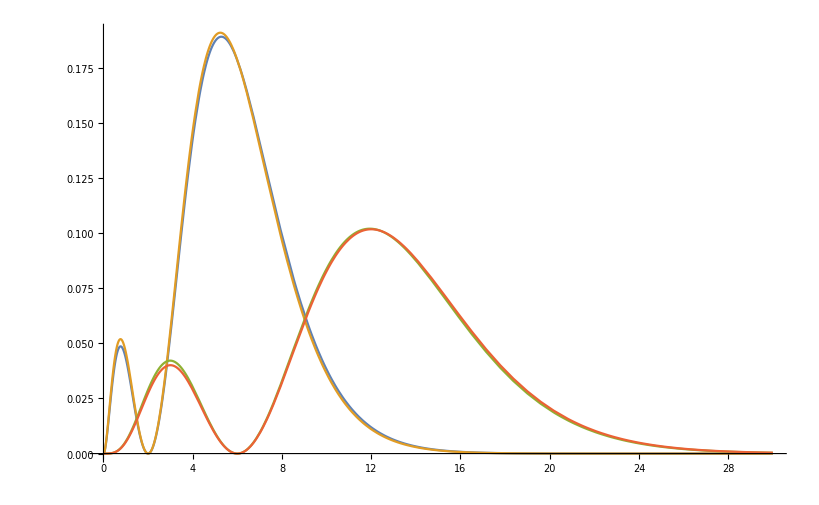

```mathematica
Plot[{Rdensity,d^2(1/(2Sqrt[2])(2-d)Exp[-d/2])^2,Rdensity2,(4/(81Sqrt[6])(6-d)d Exp[-d/3])^2d^2},{d,0,30}]
```

```mathematica
psi
```

16/81 (-2+d)^2 d^2 ⅇ^-d

```mathematica
Clear[k,c]
```

```mathematica
Rdensity
```

(409600000 (-2+d)^2 d^2 ⅇ^(-80 d/81))/3530362563